```mathematica
$MaxExtraPrecision = 25
```

```mathematica
numberOfPerticles = 8
```

8

```mathematica
numberOfFermions = numberOfPerticles / 2
```

4

```mathematica
J = Array[0 &, {numberOfPerticles, numberOfPerticles, numberOfPerticles, numberOfPerticles}]
```

{{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}}}

```mathematica
Dimensions[J]
```

```mathematica
For[a = 1, a ≤ numberOfPerticles, a++,
For[b = 1, b ≤ numberOfPerticles, b++,
For[c = 1, c ≤ numberOfPerticles, c++,
For[d = 1, d ≤ numberOfPerticles, d++,
J[[a, b, c, d]] = RandomVariate[NormalDistribution[0, 6 / (numberOfPerticles ^ 3)]]
]
]
]
]
```

```mathematica
J
```

```mathematica
For[a = 1, a ≤ numberOfPerticles, a++,
For[b = 1, b ≤ numberOfPerticles, b++,
For[c = 1, c ≤ numberOfPerticles, c++,
For[d = 1, d ≤ numberOfPerticles, d++,
If[a == b || a == c || a == d || b == c || b == d || c == d,
J[[a, b, c, d]] = 0
];

If[a < b < c< d,
J[[a, b, d, c]] = -J[[a, b, c, d]];
J[[a, c, b, d]] = -J[[a, b, c, d]];
J[[a, d, c, b]] = -J[[a, b, c, d]];

J[[b, a, c, d]] = -J[[a, b, c, d]];
J[[b, c, d, a]] = -J[[a, b, c, d]];
J[[b, d, a, c]] = -J[[a, b, c, d]];

J[[c, a, d, b]] = -J[[a, b, c, d]];
J[[c, b, a, d]] = -J[[a, b, c, d]];
J[[c, d, b, a]] = -J[[a, b, c, d]];

J[[d, a, b, c]] = -J[[a, b, c, d]];
J[[d, b, c, a]] = -J[[a, b, c, d]];
J[[d, c, a, b]] = -J[[a, b, c, d]];

J[[a, c, d, b]] = J[[a, b, c, d]];
J[[a, d, b, c]] = J[[a, b, c, d]];

J[[b, a, d, c]] = J[[a, b, c, d]];
J[[b, c, a, d]] = J[[a, b, c, d]];
J[[b, d, c, a]] = J[[a, b, c, d]];

J[[c, a, b, d]] = J[[a, b, c, d]];
J[[c, d, b, a]] = J[[a, b, c, d]];
J[[c, d, a, b]] = J[[a, b, c, d]];

J[[d, a, c, b]] = J[[a, b, c, d]];
J[[d, b, a, c]] = J[[a, b, c, d]];
J[[d, c, b, a]] = J[[a, b, c, d]];
]
]
]
]
]
```

```mathematica
J[[1,2,3,4]]
```

-0.00296182

```mathematica
J[[1,3,2,4]]
```

```mathematica
J[[1,1,1,3]]
```

```mathematica
fermionStates = {0, 1}
```

{0,1}

```mathematica
stateVectorArray = {}
```

{}

```mathematica
While[Length[stateVectorArray] !=  2^numberOfFermions,

stateVector  = RandomChoice[fermionStates, numberOfFermions];
isAlreadyContained = False;
For[j = 1, j ≤ Length[stateVectorArray], j++,
If[stateVectorArray[[j]] == stateVector,
isAlreadyContained = True;
Break;
]
];
If[isAlreadyContained == False,
AppendTo[stateVectorArray, stateVector]
]

]
```

```mathematica
Length[stateVectorArray] == 2^numberOfFermions
```

True

```mathematica
stateVectorArray = Sort[stateVectorArray]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

```mathematica
creationOperator[fermionIndex_, leftStateVector_, rightStateVector_] :=
Module[
{matrixElement},
matrixElement = 1;
For[stateIndex = 1, stateIndex ≤ Length[leftStateVector], stateIndex++,
If[fermionIndex == stateIndex,
matrixElement = matrixElement * KroneckerDelta[leftStateVector[[stateIndex]], rightStateVector[[stateIndex] ]+ 1],
matrixElement = matrixElement * KroneckerDelta[leftStateVector[[stateIndex]], rightStateVector[[stateIndex]]]
]
];
Return[matrixElement]
]
```

```mathematica
creationOperatorMatrixArray = {}
```

{}

```mathematica
For[fermionIndex = 1, fermionIndex ≤ numberOfFermions, fermionIndex++,
creationOperatorMatrix = IdentityMatrix[2^numberOfFermions];
For[left= 1, left ≤ Length[stateVectorArray], left++,
For[right = 1, right ≤ Length[stateVectorArray], right++,
leftStateVector = stateVectorArray[[left]];
rightStateVector = stateVectorArray[[right]];
creationOperatorMatrix [[left, right]] = creationOperator[fermionIndex, leftStateVector, rightStateVector];
]
];
AppendTo[creationOperatorMatrixArray, creationOperatorMatrix]
]
```

```mathematica
For[i = 1, i ≤ Length[creationOperatorMatrixArray], i++,
Print[MatrixForm[creationOperatorMatrixArray[[i]]]]
]
```

```mathematica
annihilationOperator[fermionIndex_, leftStateVector_, rightStateVector_] :=
Module[
{matrixElement},
matrixElement = 1;
For[stateIndex = 1, stateIndex ≤ Length[leftStateVector], stateIndex++,
If[fermionIndex == stateIndex,
matrixElement = matrixElement * KroneckerDelta[leftStateVector[[stateIndex]], rightStateVector[[stateIndex]] - 1],
matrixElement = matrixElement * KroneckerDelta[leftStateVector[[stateIndex]], rightStateVector[[stateIndex]]]
]
];
Return[matrixElement]
]
```

```mathematica
annihilationOperatorMatrixArray = {}
```

{}

```mathematica
For[fermionIndex = 1, fermionIndex ≤ numberOfFermions, fermionIndex++,
annihilationOperatorMatrix = IdentityMatrix[2^numberOfFermions];
For[left= 1, left ≤ Length[stateVectorArray], left++,
For[right = 1, right ≤ Length[stateVectorArray], right++,
leftStateVector = stateVectorArray[[left]];
rightStateVector = stateVectorArray[[right]];
annihilationOperatorMatrix [[left, right]] = annihilationOperator[fermionIndex, leftStateVector, rightStateVector];
]
];
AppendTo[annihilationOperatorMatrixArray, annihilationOperatorMatrix]
]
```

```mathematica
For[i = 1, i ≤ Length[annihilationOperatorMatrixArray], i++,
Print[creationOperatorMatrixArray[[i]] == ConjugateTranspose[annihilationOperatorMatrixArray[[i]]]]
]
```

True

True

True

«1 more identical outputs»

```mathematica
For[i = 1, i ≤ numberOfFermions, i++,
For[j = 1,  j ≤ numberOfFermions, j++,
If[i == j,
Print["i == j"];
Print[i];
Print[annihilationOperatorMatrixArray[[i]] . creationOperatorMatrixArray[[j]] + creationOperatorMatrixArray[[j]] .  annihilationOperatorMatrixArray[[i]] == IdentityMatrix[2^numberOfFermions]],
Print["i not equal j"];
Print[i];
Print[j];
Print[annihilationOperatorMatrixArray[[i]] . creationOperatorMatrixArray[[j]] == - creationOperatorMatrixArray[[j]] . annihilationOperatorMatrixArray[[i]]]
];
Print["--------------------------------"]
]
]
```

i == j

1

True

--------------------------------

i not equal j

1

2

False

--------------------------------

i not equal j

1

3

False

--------------------------------

i not equal j

1

4

False

--------------------------------

i not equal j

2

1

False

--------------------------------

i == j

2

True

--------------------------------

i not equal j

2

3

False

--------------------------------

i not equal j

2

4

False

--------------------------------

i not equal j

3

1

False

--------------------------------

i not equal j

3

2

False

--------------------------------

i == j

3

True

--------------------------------

i not equal j

3

4

False

--------------------------------

i not equal j

4

1

False

--------------------------------

i not equal j

4

2

False

--------------------------------

i not equal j

4

3

False

--------------------------------

i == j

4

True

--------------------------------

```mathematica
MatrixForm[annihilationOperatorMatrixArray[[3]] . creationOperatorMatrixArray[[4]]]
MatrixForm[-creationOperatorMatrixArray[[4]] . annihilationOperatorMatrixArray[[3]]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
psiArray = {}
```

{}

```mathematica
For[i = 1, i ≤ numberOfFermions, i++,

psi = (I * (annihilationOperatorMatrixArray[[i]] - creationOperatorMatrixArray[[i]])) / Sqrt[2];
AppendTo[psiArray, psi];
psi = (annihilationOperatorMatrixArray[[i]] + creationOperatorMatrixArray[[i]]) / Sqrt[2];
AppendTo[psiArray, psi];
]
```

```mathematica
For[i = 1, i ≤ numberOfPerticles, i++,
For[j = 1, j ≤ numberOfPerticles, j++,
If[i == j,
Print["i = j"];
Print[i];
Print[psiArray[[i]] . psiArray[[j]] == 1/2 * IdentityMatrix[2^numberOfFermions]],
Print["i not equal j"];
Print[i];
Print[j];
Print[psiArray[[i]] . psiArray[[j]] == - psiArray[[j]] . psiArray[[i]]]
];
Print["--------------------------------"]
]
]
```

i = j

1

True

--------------------------------

i not equal j

1

2

True

--------------------------------

i not equal j

1

3

False

--------------------------------

i not equal j

1

4

False

--------------------------------

i not equal j

1

5

False

--------------------------------

i not equal j

1

6

False

--------------------------------

i not equal j

1

7

False

--------------------------------

i not equal j

1

8

False

--------------------------------

i not equal j

2

1

True

--------------------------------

i = j

2

True

--------------------------------

i not equal j

2

3

False

--------------------------------

i not equal j

2

4

False

--------------------------------

i not equal j

2

5

False

--------------------------------

i not equal j

2

6

False

--------------------------------

i not equal j

2

7

False

--------------------------------

i not equal j

2

8

False

--------------------------------

i not equal j

3

1

False

--------------------------------

i not equal j

3

2

False

--------------------------------

i = j

3

True

--------------------------------

i not equal j

3

4

True

--------------------------------

i not equal j

3

5

False

--------------------------------

i not equal j

3

6

False

--------------------------------

i not equal j

3

7

False

--------------------------------

i not equal j

3

8

False

--------------------------------

i not equal j

4

1

False

--------------------------------

i not equal j

4

2

False

--------------------------------

i not equal j

4

3

True

--------------------------------

i = j

4

True

--------------------------------

i not equal j

4

5

False

--------------------------------

i not equal j

4

6

False

--------------------------------

i not equal j

4

7

False

--------------------------------

i not equal j

4

8

False

--------------------------------

i not equal j

5

1

False

--------------------------------

i not equal j

5

2

False

--------------------------------

i not equal j

5

3

False

--------------------------------

i not equal j

5

4

False

--------------------------------

i = j

5

True

--------------------------------

i not equal j

5

6

True

--------------------------------

i not equal j

5

7

False

--------------------------------

i not equal j

5

8

False

--------------------------------

i not equal j

6

1

False

--------------------------------

i not equal j

6

2

False

--------------------------------

i not equal j

6

3

False

--------------------------------

i not equal j

6

4

False

--------------------------------

i not equal j

6

5

True

--------------------------------

i = j

6

True

--------------------------------

i not equal j

6

7

False

--------------------------------

i not equal j

6

8

False

--------------------------------

i not equal j

7

1

False

--------------------------------

i not equal j

7

2

False

--------------------------------

i not equal j

7

3

False

--------------------------------

i not equal j

7

4

False

--------------------------------

i not equal j

7

5

False

--------------------------------

i not equal j

7

6

False

--------------------------------

i = j

7

True

--------------------------------

i not equal j

7

8

True

--------------------------------

i not equal j

8

1

False

--------------------------------

i not equal j

8

2

False

--------------------------------

i not equal j

8

3

False

--------------------------------

i not equal j

8

4

False

--------------------------------

i not equal j

8

5

False

--------------------------------

i not equal j

8

6

False

--------------------------------

i not equal j

8

7

True

--------------------------------

i = j

8

True

--------------------------------

```mathematica
MatrixForm[psiArray[[8]] . psiArray[[6]]]
MatrixForm[-psiArray[[6]] . psiArray[[8]]]
```

(0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0)

(0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0)

True

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2)
-ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Length[psiArray] == numberOfPerticles
```

True

```mathematica
PartialHamiltonian[a_, b_, c_, d_] :=
Module[
{},
Return[(I * J[[a,b,c,d]] / Factorial[numberOfPerticles])* psiArray[[a]] . psiArray[[b]] . psiArray[[c]] . psiArray[[d]]]
]
```

```mathematica
Hamiltonian = ParallelSum[PartialHamiltonian[a,b,c,d], {a, numberOfPerticles}, {b, numberOfPerticles},{c, numberOfPerticles},{d, numberOfPerticles}]
```

```mathematica
PartialHamiltonian[1,2,3,4]
```

```mathematica
Hamiltonian = Array[0 &, {2^numberOfFermions, 2^numberOfFermions}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
For[a = 1, a ≤ numberOfPerticles, a++,
Print[a];
For[b = 1, b ≤ numberOfPerticles, b++,
For[c = 1, c ≤ numberOfPerticles, c++,
For[d = 1, d ≤ numberOfPerticles, d++,
Hamiltonian = Hamiltonian + PartialHamiltonian[a, b, c, d]
]
]
]
]
```

1

2

3

4

5

6

7

8

```mathematica
MatrixForm[Hamiltonian]
```

(0.+1.21533×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -5.10219×10^-7+1.45911×10^-7 ⅈ | 0.+0. ⅈ | 4.37672×10^-7-9.13088×10^-8 ⅈ | 2.2211×10^-8-1.23865×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.20776×10^-7-1.72358×10^-8 ⅈ | -1.81629×10^-7+7.25901×10^-8 ⅈ | 0.+0. ⅈ | 5.06714×10^-7-7.0111×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 4.62273×10^-8+9.86217×10^-8 ⅈ
0.+0. ⅈ | 0.+1.15026×10^-6 ⅈ | -2.03947×10^-7+1.8174×10^-7 ⅈ | 0.+0. ⅈ | 1.71586×10^-9+3.24345×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 4.93076×10^-8+8.50632×10^-8 ⅈ | -7.91496×10^-8+1.86212×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.2895×10^-7-2.70915×10^-8 ⅈ | 0.+0. ⅈ | -1.4122×10^-7-1.86936×10^-8 ⅈ | -1.84011×10^-7+6.00639×10^-8 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -2.03947×10^-7-1.8174×10^-7 ⅈ | 0.-5.60741×10^-7 ⅈ | 0.+0. ⅈ | -1.8912×10^-8+2.29276×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.1065×10^-7+3.57525×10^-7 ⅈ | -1.87139×10^-7+2.18026×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -3.27686×10^-7+4.94749×10^-8 ⅈ | 0.+0. ⅈ | 2.11773×10^-7-1.14615×10^-7 ⅈ | 1.4122×10^-7+1.86936×10^-8 ⅈ | 0.+0. ⅈ
-5.10219×10^-7-1.45911×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.-3.47516×10^-6 ⅈ | 0.+0. ⅈ | 8.84077×10^-8-3.06834×10^-8 ⅈ | -4.00836×10^-7+1.08879×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -8.71094×10^-8-3.05236×10^-7 ⅈ | -8.49761×10^-8+2.92485×10^-7 ⅈ | 0.+0. ⅈ | 3.70404×10^-7-4.64828×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -5.06714×10^-7+7.0111×10^-8 ⅈ
0.+0. ⅈ | 1.71586×10^-9-3.24345×10^-7 ⅈ | -1.8912×10^-8-2.29276×10^-7 ⅈ | 0.+0. ⅈ | 0.+1.44497×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -8.15941×10^-8+6.53667×10^-8 ⅈ | 2.36032×10^-7+2.23476×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.52137×10^-7-4.20694×10^-7 ⅈ | 0.+0. ⅈ | 3.27686×10^-7-4.94749×10^-8 ⅈ | -1.2895×10^-7+2.70915×10^-8 ⅈ | 0.+0. ⅈ
4.37672×10^-7+9.13088×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 8.84077×10^-8+3.06834×10^-8 ⅈ | 0.+0. ⅈ | 0.+1.29523×10^-7 ⅈ | -1.7324×10^-7+7.17513×10^-10 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -3.16432×10^-7+1.33867×10^-7 ⅈ | -5.5275×10^-8-1.76459×10^-7 ⅈ | 0.+0. ⅈ | 8.49761×10^-8-2.92485×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.81629×10^-7-7.25901×10^-8 ⅈ
2.2211×10^-8+1.23865×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -4.00836×10^-7-1.08879×10^-7 ⅈ | 0.+0. ⅈ | -1.7324×10^-7-7.17513×10^-10 ⅈ | 0.+2.13031×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -3.98204×10^-7-1.01413×10^-9 ⅈ | 3.16432×10^-7-1.33867×10^-7 ⅈ | 0.+0. ⅈ | 8.71094×10^-8+3.05236×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.20776×10^-7+1.72358×10^-8 ⅈ
0.+0. ⅈ | 4.93076×10^-8-8.50632×10^-8 ⅈ | 1.1065×10^-7-3.57525×10^-7 ⅈ | 0.+0. ⅈ | -8.15941×10^-8-6.53667×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.-2.03448×10^-6 ⅈ | 2.91597×10^-7-2.40412×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.36032×10^-7-2.23476×10^-7 ⅈ | 0.+0. ⅈ | 1.87139×10^-7-2.18026×10^-7 ⅈ | 7.91496×10^-8-1.86212×10^-7 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -7.91496×10^-8-1.86212×10^-7 ⅈ | -1.87139×10^-7-2.18026×10^-7 ⅈ | 0.+0. ⅈ | 2.36032×10^-7-2.23476×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.91597×10^-7-2.40412×10^-7 ⅈ | 0.-2.03448×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 8.15941×10^-8-6.53667×10^-8 ⅈ | 0.+0. ⅈ | -1.1065×10^-7-3.57525×10^-7 ⅈ | -4.93076×10^-8-8.50632×10^-8 ⅈ | 0.+0. ⅈ
1.20776×10^-7+1.72358×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -8.71094×10^-8+3.05236×10^-7 ⅈ | 0.+0. ⅈ | -3.16432×10^-7-1.33867×10^-7 ⅈ | 3.98204×10^-7-1.01413×10^-9 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+2.13031×10^-6 ⅈ | 1.7324×10^-7-7.17513×10^-10 ⅈ | 0.+0. ⅈ | 4.00836×10^-7-1.08879×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.2211×10^-8+1.23865×10^-7 ⅈ
-1.81629×10^-7-7.25901×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -8.49761×10^-8-2.92485×10^-7 ⅈ | 0.+0. ⅈ | 5.5275×10^-8-1.76459×10^-7 ⅈ | 3.16432×10^-7+1.33867×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.7324×10^-7+7.17513×10^-10 ⅈ | 0.+1.29523×10^-7 ⅈ | 0.+0. ⅈ | -8.84077×10^-8+3.06834×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -4.37672×10^-7+9.13088×10^-8 ⅈ
0.+0. ⅈ | 1.2895×10^-7+2.70915×10^-8 ⅈ | -3.27686×10^-7-4.94749×10^-8 ⅈ | 0.+0. ⅈ | 1.52137×10^-7-4.20694×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.36032×10^-7+2.23476×10^-7 ⅈ | 8.15941×10^-8+6.53667×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+1.44497×10^-6 ⅈ | 0.+0. ⅈ | 1.8912×10^-8-2.29276×10^-7 ⅈ | -1.71586×10^-9-3.24345×10^-7 ⅈ | 0.+0. ⅈ
5.06714×10^-7+7.0111×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -3.70404×10^-7-4.64828×10^-7 ⅈ | 0.+0. ⅈ | 8.49761×10^-8+2.92485×10^-7 ⅈ | 8.71094×10^-8-3.05236×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 4.00836×10^-7+1.08879×10^-7 ⅈ | -8.84077×10^-8-3.06834×10^-8 ⅈ | 0.+0. ⅈ | 0.-3.47516×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 5.10219×10^-7-1.45911×10^-7 ⅈ
0.+0. ⅈ | -1.4122×10^-7+1.86936×10^-8 ⅈ | -2.11773×10^-7-1.14615×10^-7 ⅈ | 0.+0. ⅈ | 3.27686×10^-7+4.94749×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.87139×10^-7+2.18026×10^-7 ⅈ | -1.1065×10^-7+3.57525×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.8912×10^-8+2.29276×10^-7 ⅈ | 0.+0. ⅈ | 0.-5.60741×10^-7 ⅈ | 2.03947×10^-7-1.8174×10^-7 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.84011×10^-7+6.00639×10^-8 ⅈ | 1.4122×10^-7-1.86936×10^-8 ⅈ | 0.+0. ⅈ | -1.2895×10^-7-2.70915×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 7.91496×10^-8+1.86212×10^-7 ⅈ | -4.93076×10^-8+8.50632×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.71586×10^-9+3.24345×10^-7 ⅈ | 0.+0. ⅈ | 2.03947×10^-7+1.8174×10^-7 ⅈ | 0.+1.15026×10^-6 ⅈ | 0.+0. ⅈ
-4.62273×10^-8+9.86217×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -5.06714×10^-7-7.0111×10^-8 ⅈ | 0.+0. ⅈ | 1.81629×10^-7+7.25901×10^-8 ⅈ | -1.20776×10^-7-1.72358×10^-8 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.2211×10^-8-1.23865×10^-7 ⅈ | -4.37672×10^-7-9.13088×10^-8 ⅈ | 0.+0. ⅈ | 5.10219×10^-7+1.45911×10^-7 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+1.21533×10^-6 ⅈ)

```mathematica
eigenValues = Eigenvalues[Hamiltonian]
```

{2.5411×10^-21-4.03627×10^-6 ⅈ,-7.75953×10^-22-2.46984×10^-6 ⅈ,-5.64965×10^-22+2.34511×10^-6 ⅈ,-1.74535×10^-21-2.06062×10^-6 ⅈ,-3.07759×10^-22+1.64454×10^-6 ⅈ,-6.1498×10^-22+1.61799×10^-6 ⅈ,-2.60505×10^-23-1.58714×10^-6 ⅈ,3.89434×10^-22+1.2956×10^-6 ⅈ,2.89998×10^-22+1.09284×10^-6 ⅈ,3.34133×10^-7+9.35796×10^-7 ⅈ,-3.34133×10^-7+9.35796×10^-7 ⅈ,-6.16565×10^-7+7.24648×10^-7 ⅈ,6.16565×10^-7+7.24648×10^-7 ⅈ,9.40946×10^-22-8.75233×10^-7 ⅈ,9.64001×10^-23-2.88738×10^-7 ⅈ,-4.73181×10^-22+8.75113×10^-10 ⅈ}

```mathematica
Hamiltonian == ConjugateTranspose[Hamiltonian]
```

False

```mathematica
Length[eigenValues]
```

32

```mathematica
For[i = 1, i ≤ Length[eigenValues], i++,
For[j = i + 1, j ≤ Length[eigenValues], j++,
If[Hamiltonian[[i,j]] ≠ Conjugate[Hamiltonian[[j,i]]],
Print[i];
Print[j];
Print["---------------------"]
]
]
]
```

1

16

---------------------

2

15

---------------------

3

14

---------------------

4

13

---------------------

5

12

---------------------

6

11

---------------------

7

10

---------------------

8

9

---------------------

```mathematica
Hamiltonian[[1,16]]
Conjugate[Hamiltonian[[16,1]]]
```

4.62273×10^-8+9.86217×10^-8 ⅈ

-4.62273×10^-8-9.86217×10^-8 ⅈ

```mathematica
realEigenValues
```

{-2.4417×10^-6,-2.00049×10^-6,1.67855×10^-6,-1.19054×10^-6,4.71419×10^-7,4.71419×10^-7,9.93978×10^-7,9.93978×10^-7,7.57615×10^-7,-6.11448×10^-7,-6.11448×10^-7,5.58935×10^-7,5.58935×10^-7,3.52726×10^-7,2.78057×10^-7,-2.59985×10^-7}

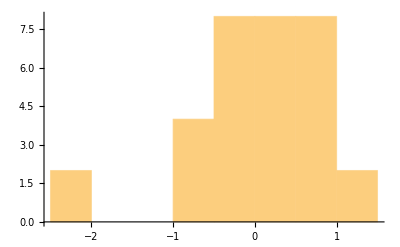

```mathematica
Histogram[realEigenValues, 10]
```

```mathematica
MatrixForm[psiArray[[1]] . psiArray[[2]] + psiArray[[2]] . psiArray[[1]]]
```

```mathematica
Length[psiArray]
```